```mathematica
Clear[phystest];
Clear[zero];
Clear[Σ];
Clear[s];
Clear[d];
Clear[g];
Clear[λ];
Clear[a];
Clear[b];
Clear[cp];
Clear[cm];
Clear[covm];
```

```mathematica
zero={{0,0},{0,0}};
```

```mathematica
Σ=ArrayFlatten[{{ⅈ PauliMatrix[2],zero},{zero,ⅈ PauliMatrix[2]}}];
```

```mathematica
s=Table[RandomReal[{1,400}],{i,10^5}];
(*I changed the max random value of s from 100 to 400*)
d=Table[RandomReal[{0,s[[i]]-1}],{i,10^5}];
g=Table[RandomReal[{2 Abs[d[[i]]]+1,2s[[i]]-1}],{i,10^5}];
λ=Table[RandomReal[{-1,1}],{i,10^5}];

a=Table[s[[i]]+d[[i]],{i,10^5}];

b=Table[s[[i]]-d[[i]],{i,10^5}];


cp=Table[
1/(4 √(s[[i]]^2-d[[i]]^2))*(√((4 d[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2)+√((4 s[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2))
,{i,10^5}]//FullSimplify;

cm=Table[
1/(4 √(s[[i]]^2-d[[i]]^2))*(√((4 d[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2)-√((4 s[[i]]^2+1/2(g[[i]]^2+1)(λ[[i]]-1)-(2 d[[i]]^2+g[[i]])(λ[[i]]+1))^2-4 g[[i]]^2))
,{i,10^5}]//FullSimplify;
```

```mathematica
cp[[1]]
```

88.4345

```mathematica
covm=Table[{{a[[i]],0,cp[[i]],0},{0,a[[i]],0,cm[[i]]},{cp[[i]],0,b[[i]],0},{0,cm[[i]],0,b[[i]]}},{i,10^5}];
```

```mathematica
covm[[4]]
```

{{102.401,0,88.6419,0},{0,102.401,0,10.8908},{88.6419,0,76.7702,0},{0,10.8908,0,76.7702}}

{{9.05891,0,-1.80664,0},{0,9.05891,0,-3.84297},{-1.80664,0,5.39379,0},{0,-3.84297,0,5.39379}}

```mathematica
Clear[phystest]
```

```mathematica
phystest={};
Do[AppendTo[phystest,{Eigenvalues[covm[[i]]],Eigenvalues[covm[[i]]+ⅈ Σ],Abs[Eigenvalues[ⅈ Σ . covm[[i]]//Chop]]}];,{i,1,Length[covm]}]
```

```mathematica
Length[phystest]
```

100000

```mathematica
phystest[[1]]
```

{{188.211,175.909,12.3226,0.0206641},{188.227,175.903,12.3286,0.00478206},{80.4869,80.4869,1.14078,1.14078}}

```mathematica
{1,Min[phystest[[1,1]]]}
```

{1,0.0206641}

```mathematica
Table[{i,Min[phystest[[i,1]]]},{i,1,Length[cm]}];
```

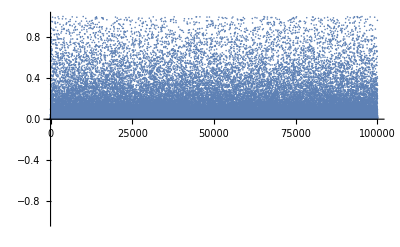

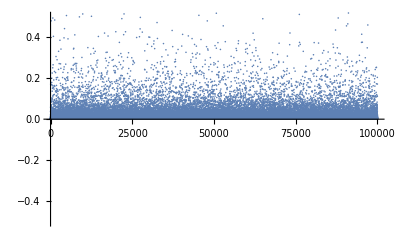

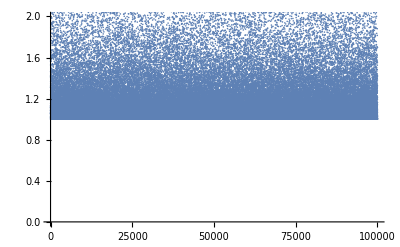

```mathematica
ListPlot[Table[{i,Min[phystest[[i,1]]]},{i,1,Length[cm]}],PlotRange->{-1,1}]
ListPlot[Table[{i,Min[phystest[[i,2]]]},{i,1,Length[cm]}],PlotRange->{-0.5,0.5}]
ListPlot[Table[{i,Min[phystest[[i,3]]]},{i,1,Length[cm]}],PlotRange->{0,2}]
```

```mathematica
covmpt=Table[{{a[[i]],0,cp[[i]],0},{0,a[[i]],0,-cm[[i]]},{cp[[i]],0,b[[i]],0},{0,-cm[[i]],0,b[[i]]}},{i,10^5}];
```

```mathematica
(*partially transposed cov matrix)
```

```mathematica
phystest2={};
Do[AppendTo[phystest2,{Abs[Eigenvalues[ⅈ Σ . covmpt[[i]]//Chop]]}];,{i,1,Length[covmpt]}]


phystest2[[200]]
```

{{144.562,144.562,0.948294,0.948294}}

```mathematica
Table[{i,{Min[phystest2[[i]]]}},{i,1,Length[cm]}];
Min[phystest2[[1]]]
```

0.258571

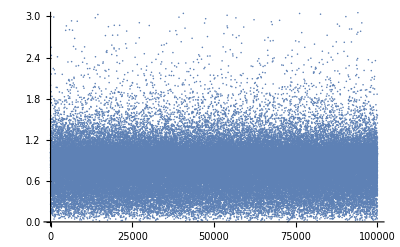

```mathematica
ListPlot[Table[{i,Min[phystest2[[i]]]},{i,10^5}],PlotRange->{0,3}]
(*Points that are less than 1 are entangled and greater than one are seperable*)
```

```mathematica
SympEig={};
Do[AppendTo[SympEig,Min[Abs[Eigenvalues[ⅈ Σ . covmpt[[i]]]]//Chop]];,{i,10^5}];
```

```mathematica
Dynamic[i]
```

```mathematica
SympEig[[1]]
```

0.504792

```mathematica
Table[{i,{SympEig[[i]]}},{i,10^5}];
```

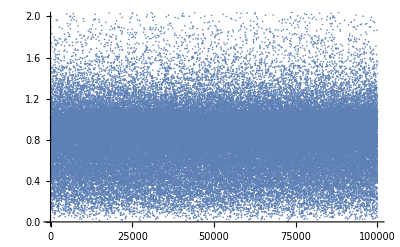

```mathematica
ListPlot[Table[{i,SympEig[[i]]},{i,10^5}],PlotRange->{0,2}]
```

```mathematica
Negativity={};
Do[AppendTo[Negativity,(1-SympEig[[i]])/(2SympEig[[i]])];,{i,10^5}];
Negativity[[1]]
```

1.4337

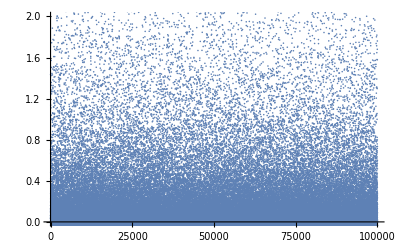

```mathematica
Table[{i,{Negativity[[i]]}},{i,10^5}];
ListPlot[Table[{i,Negativity[[i]]},{i,10^5}],PlotRange->{0,2}]
```

```mathematica
LogNeg={};
Do[AppendTo[LogNeg,-Log[SympEig[[i]]]];,{i,10^5}];
LogNeg[[1]]
```

1.35258

```mathematica
Dynamic[i]
```

```mathematica
Table[{i,{LogNeg[[i]]}},{i,10^5}];
```

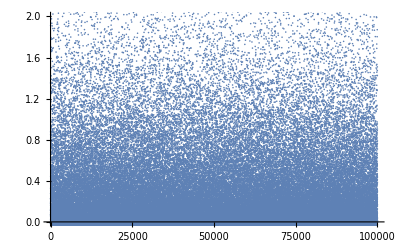

```mathematica
ListPlot[Table[{i,LogNeg[[i]]},{i,10^5}],PlotRange->{0,2}]
```

```mathematica
Subscript[Determinantσ, P.T]={};
```

```mathematica
Do[AppendTo[Subscript[Determinantσ, P.T],(a[[i]]b[[i]]-cp[[i]]^2)(a[[i]]b[[i]]-cm[[i]]^2)];,{i,10^5}];
Subscript[Determinantσ, P.T][[1]]
```

951.141

```mathematica
Table[{i,{Determinantσ[[i]]}},{i,10^5}];
```

```mathematica
Purity={};
```

```mathematica
Do[AppendTo[Purity,1/(√(Subscript[Determinantσ, P.T][[i]]))];,{i,10^5}];
```

```mathematica
Purity[[1]]
```

0.0108912

```mathematica
Table[{i,{Purity[[i]]}},{i,10^5}];
```

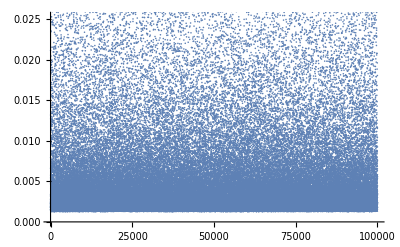

```mathematica
ListPlot[Table[{i,Purity[[i]]},{i,10^5}]]
```

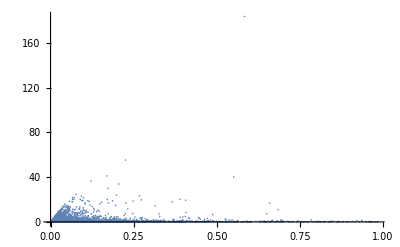

```mathematica
ListPlot[Table[{Purity[[i]],Max[0,Negativity[[i]]]},{i,10^5}],PlotRange->All]
(*Yesterday max value on y axis was about 40, now is nearly 200*)
```

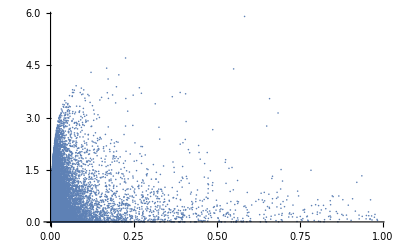

```mathematica
ListPlot[Table[{Purity[[i]],Max[0,LogNeg[[i]]]},{i,10^5}],PlotRange->All]
(*Yesterday max value on y axis was about 4, now is around 6*)
```